```mathematica
H=10^-8;
calPf=1/(2ϵfs)(H/(2π))^2
```

1/(80000000000000000 π^2 ϵfs)

```mathematica
ϵf=ϵfs/.Solve[calPf==10^-3,ϵfs][[1]];ϵf//N
```

1.26651×10^-15

```mathematica
ϵf
```

1/(80000000000000 π^2)

```mathematica
8 10^13
```

80000000000000

```mathematica
ϵi=10^-2;
```

```mathematica
Nf=Log[ϵi/ϵf]/6;Nf//N
```

4.94956

```mathematica
dotx0=dotx0s/.Solve[ϵi==dotx0s^2/(2 H^2),dotx0s][[2]]
dotxf=dotxfs/.Solve[ϵf==dotxfs^2/(2 H^2),dotxfs][[2]]
```

1/(500000000 √2)

1/(200000000000000 √10 π)

```mathematica
5 10^8
2 10^14
```

500000000

200000000000000

```mathematica
xf=(dotx0-dotxf)/(3H);xf//N
```

0.0471404

```mathematica
xf/(H/(2π))//N
```

2.96192×10^7

```mathematica
B[NN_]=(2π xf)/H-(2π dotx0)/(3 H^2)(1-E^(-3NN));
P0[x_,NN_]=1/Sqrt[2π NN] Exp[-x^2/(2NN)];
```

```mathematica
g1[NN_]=(B[NN]/NN-2B'[NN])P0[B[NN],NN]//Simplify
g2[N1_,N2_]=(2B'[N1]-(B[N1]-B[N2])/(N1-N2))P0[B[N1]-B[N2],N1-N2]//Simplify
```

(ⅇ^(-(500+27 NN^2-400000000 √5 ⅇ^(-3 NN) π+400000000000000 ⅇ^(-6 NN) π^2)/(9 NN)) (-10 √5 ⅇ^(3 NN)+20000000 (π+6 NN π)))/(3 NN^(3/2) √π)

(20000000 ⅇ^(-3 N1-3 N2-(400000000000000 ⅇ^(-6 (N1+N2)) (ⅇ^(3 N1)-ⅇ^(3 N2))^2 π^2)/(9 (N1-N2))) (ⅇ^(3 N1)+ⅇ^(3 N2) (-1-6 N1+6 N2)) √π)/(3 (N1-N2)^(3/2))

```mathematica
DN=1/200;
NList=Table[NN,{NN,3,11,DN}];
Length[NList]
```

1601

```mathematica
Delta=ParallelTable[If[j>i,0,If[j==i,Re[1/2 NIntegrate[g2[NList[[i]],Np],{Np,NList[[i]]-DN,NList[[i]]}]]//Quiet,N[DN/2 g2[NList[[i]],NList[[j]]-DN/2]]//Quiet]],{i,Length[NList]},{j,Length[NList]}];//AbsoluteTiming
```

{32.7899,Null}

```mathematica
FPFTList=Table[0,{i,Length[NList]}];
```

```mathematica
FPFTList[[1]]={NList[[1]],0};
FPFTList[[2]]={NList[[2]],g1[NList[[2]]](1-Delta[[2,2]])^-1}//Quiet;
For[i=3,i≤Length[FPFTList],i++,
FPFTList[[i]]={NList[[i]],(1-Delta[[i,i]])^-1(g1[NList[[i]]]+ParallelSum[FPFTList[[j,2]](Delta[[i,j]]+Delta[[i,j+1]])//Quiet,{j,2,i-1}])}//Quiet;]//AbsoluteTiming
```

{113.175,Null}

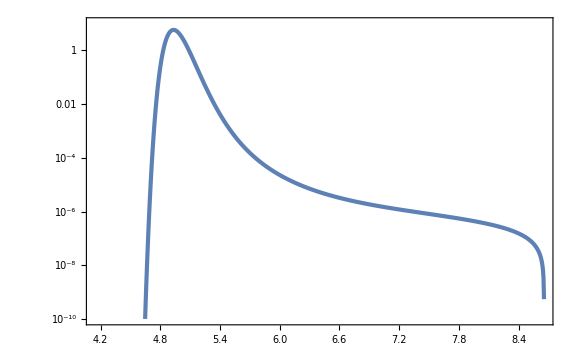

```mathematica
ListLogPlot[FPFTList,PlotRange->{10^-10,10}]
```

```mathematica
Nmin=4.5;
Nmax=9;
```

```mathematica
FPFTint[NN_]=Interpolation[FPFTList,InterpolationOrder->1][NN];
```

```mathematica
NIntegrate[FPFTint[NN],{NN,Nmin,Nmax}]
Nmean=NIntegrate[NN FPFTint[NN],{NN,Nmin,Nmax}]
varZ=NIntegrate[(NN-Nmean)^2 FPFTint[NN],{NN,Nmin,Nmax}]
Z3=NIntegrate[(NN-Nmean)^3 FPFTint[NN],{NN,Nmin,Nmax}]
Z4=NIntegrate[(NN-Nmean)^4 FPFTint[NN],{NN,Nmin,Nmax}]-3 varZ^2
fNL=5/18 Z3/varZ^2
```

1.00525

4.98304

0.00649937

-0.0000455492

0.0000927334

-0.299527

```mathematica
Nf//N
```

4.94956

```mathematica
H3[x_]=x^3-3x;
H4[x_]=x^4-6 x^2+3;
```

```mathematica
Z3fNL=18/5 varZ^2 5/2
```

0.000380176

```mathematica
FPFTGauss[NN_]=1/Sqrt[2π varZ] Exp[(-(NN-Nmean)^2)/(2varZ)];
FPFTEdge[NN_]=(1+1/(3 2)Z3/varZ^(3/2)H3[(NN-Nmean)/Sqrt[varZ]]+1/(4 3 2)Z4/varZ^2 H4[(NN-Nmean)/Sqrt[varZ]])FPFTGauss[NN];
FPFTEdgefNL[NN_]=(1+1/(3 2)Z3fNL/varZ^(3/2)H3[(NN-Nmean)/Sqrt[varZ]])FPFTGauss[NN];
```

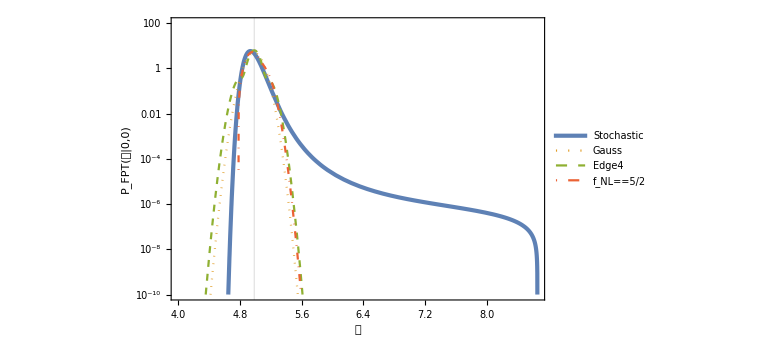

```mathematica
LogPlot[{FPFTint[NN],FPFTGauss[NN],FPFTEdge[NN],FPFTEdgefNL[NN]},{NN,4,9},PlotStyle->{AbsoluteThickness[3],Dotted,Dashed,DotDashed},PlotRange->{10^-10,10^2},FrameLabel->{𝒩,Subscript[P, FPT][𝒩|0,0]},GridLines->{{Nmean},None},PlotLegends->Placed[LineLegend[{"Stochastic","Gauss","Edge4",Subscript[f, NL]==5/2},LabelStyle->Directive[Black,Larger,FontFamily->"Palatino"]],{0.75,0.75}]]
```

```mathematica
FPFTint[Nmean+1]//ScientificForm
```

2.50253×10^-5

```mathematica
Ndrop=NN/.FindRoot[FPFTint[NN]==10^-9,{NN,7.4}]
```

8.65423

General::munfl: Exp[-3672.22] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2130.54] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1223.75] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

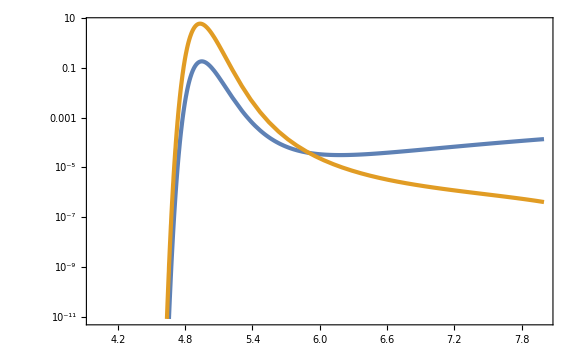

```mathematica
LogPlot[{P0[B[NN],NN],FPFTint[NN]},{NN,4,8}]
```

```mathematica
NIntegrate[FPFTGauss[NN],{NN,Nmin,Nmax}]
NIntegrate[NN FPFTGauss[NN],{NN,Nmin,Nmax}]/Nmean
NIntegrate[(NN-Nmean)^2 FPFTGauss[NN],{NN,Nmin,Nmax}]/varZ
NIntegrate[(NN-Nmean)^3 FPFTGauss[NN],{NN,Nmin,Nmax}]/Z3
```

1.

1.

1.

-2.7856×10^-6

```mathematica
NIntegrate[FPFTEdge[NN],{NN,Nmin,Nmax}]
NIntegrate[NN FPFTEdge[NN],{NN,Nmin,Nmax}]/Nmean
NIntegrate[(NN-Nmean)^2 FPFTEdge[NN],{NN,Nmin,Nmax}]/varZ
NIntegrate[(NN-Nmean)^3 FPFTEdge[NN],{NN,Nmin,Nmax}]/Z3
(NIntegrate[(NN-Nmean)^4 FPFTEdge[NN],{NN,Nmin,Nmax}]-3 varZ^2)/Z4
```

1.

1.

0.999995

0.999677

0.999921

```mathematica
PFP[x_,NN_]:=(P0[x,NN]-NIntegrate[FPFTint[Np]P0[x-B[Np],NN-Np],{Np,0,NN}])UnitStep[B[NN]-x]
```

```mathematica
PFP6List=ParallelTable[{x,PFP[x,6]//Quiet},{x,-3 6,B[6],1/100}];//AbsoluteTiming
```

{156.037,Null}

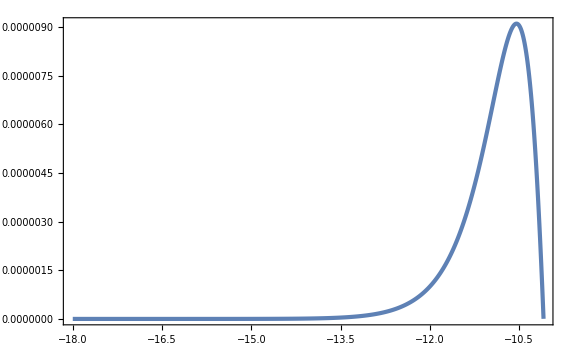

```mathematica
ListPlot[PFP6List,PlotRange->Full]
```

```mathematica
PFP6int[x_]=Interpolation[PFP6List][x];
```

```mathematica
NIntegrate[PFP6int[x],{x,-3 6,B[6]}]
```

InterpolatingFunction::dmvali: The integration endpoint -20000000/3 √2 (1-1/ⅇ^18) π+20000000000000000/3 (1/(500000000 √2)-1/(200000000000000 √10 π)) π in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

9.91418×10^-6

```mathematica
PR[zeta_,NR_]:=PFP[B[zeta+Nf],zeta+Nf-NR]
```

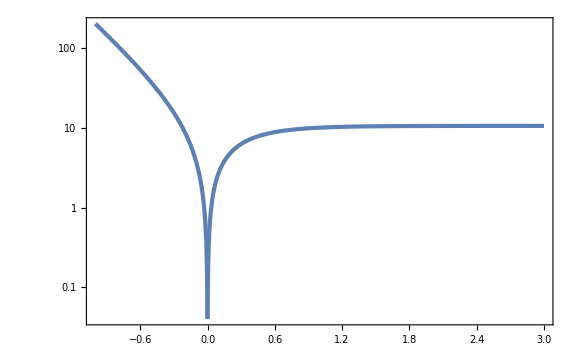

```mathematica
LogPlot[Abs[B[zeta+Nf]],{zeta,-1,3},PlotRange->Full]
```

```mathematica
zetamin[NR_]=NR-Nf;
```

```mathematica
zetamin[3]//N
```

-1.94956

```mathematica
PR[10,3]//Quiet
```

5.24715×10^-6

```mathematica
PR3List=ParallelTable[{zeta,PR[zeta,3]//Quiet},{zeta,-1,3,1/100}];//AbsoluteTiming
```

{20.6656,Null}

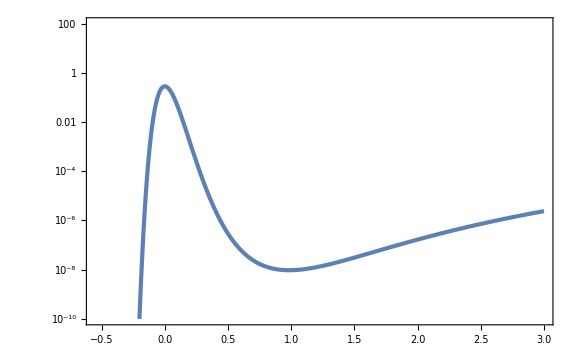

```mathematica
ListLogPlot[PR3List,PlotRange->{10^-10,10^2}]
```

```mathematica
PR3int[zeta_]=Interpolation[PR3List,InterpolationOrder->1][zeta];
```

```mathematica
Norm3=NIntegrate[PR3int[zeta],{zeta,-1,3}]
```

General::munfl: 1.29646×10^-306 (-0.01) is too small to represent as a normalized machine number; precision may be lost.

0.032382

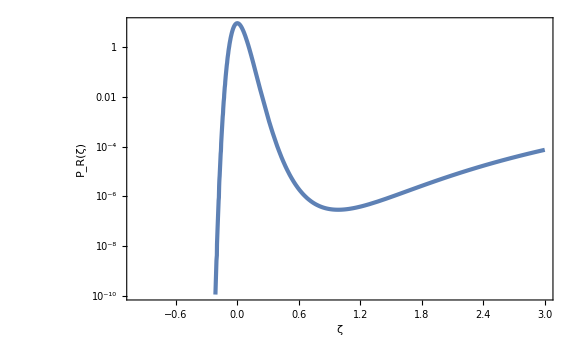

```mathematica
LogPlot[1/Norm3 PR3int[zeta],{zeta,-1,3},FrameLabel->{{Subscript[P, R][ζ],None},{ζ,Subscript[N, bw][R]==3}}]
```

```mathematica
zetamin[0]//N
```

-4.94956

```mathematica
PR[5,0]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in Np near {Np} = {5.13009}. NIntegrate obtained 0.000473562 and 1.96354×10^-8 for the integral and error estimates.

1.80601×10^-6

```mathematica
PR0List=ParallelTable[{zeta,PR[zeta,0]//Quiet},{zeta,-1,3,1/100}];//AbsoluteTiming
```

{102.387,Null}

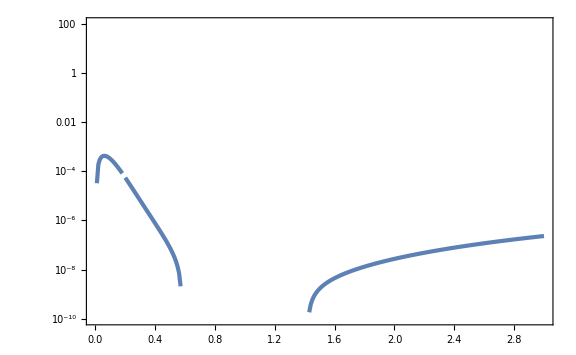

```mathematica
ListLogPlot[PR0List,PlotRange->{10^-10,10^2}]
```